Reference: John C. Tully, JCP 93, 1061 (1990)

```mathematica
ClearAll["Global`*"]
```

PARAMETERS FROM TULLY PAPER:

```mathematica
A0 = 0.01;
B0=1.6;
C0 = 0.005;
D0 = 1.0;
```

INITIAL CONDITIONS:

```mathematica
x0=-10.0;
v0=0.5;
dt=0.1;
c1=0.8;
c2=0.6;
ℏ=1;
m=1;
trange=50;
```

Xvals -> list of x values at each t; PotVals -> list of adiabatic potential values at each t

```mathematica
Xvals=Range[trange];
PotVals=Range[trange];
```

MATRIX:

```mathematica
Vplus = ({{A0(1-ⅇ^(-B0 x)), C0 ⅇ^(-D0 x^2)}, {C0 ⅇ^(-D0 x^2), -A0(1-ⅇ^(-B0 x))}});
Vminus = ({{-A0(1-ⅇ^(B0 x)), C0 ⅇ^(-D0 x^2)}, {C0 ⅇ^(-D0 x^2), A0(1-ⅇ^(B0 x))}});
```

MATRIX ELEMENTS:

```mathematica
V11[x_]:=If[x>=0,A0(1-ⅇ^(-B0 x)),-A0(1-ⅇ^(B0 x))];
```

```mathematica
V22[x_]:=-V11[x];
```

```mathematica
V12[x_]:=C0 ⅇ^(-D0 x^2);
```

```mathematica
V21[x_]:=V12[x];
```

POSITIVE/NEGATIVE EIGENVALUES:

```mathematica
{ϵ1p[x_],ϵ2p[x_]} = Eigenvalues[Vplus];
{ϵ1m[x_],ϵ2m[x_]} = Eigenvalues[Vminus];
```

POSITIVE/NEGATIVE EIGENVECTORS:

```mathematica
{{E1p[x_],E2p[x_]},{E3p[x_],E4p[x_]}}=Eigenvectors[Vplus];
```

```mathematica
{{E1m[x_],E2m[x_]},{E3m[x_],E4m[x_]}}=Eigenvectors[Vminus];
```

NORMALIZE EIGENVECTORS:

```mathematica
E1Normp[x_]:=(E1p[x]+E2p[x])/Sqrt[E1p[x]^2+E2p[x]^2];
```

```mathematica
E1Normm[x_]:=(E1m[x]+E2m[x])/Sqrt[E1m[x]^2+E2m[x]^2];
```

```mathematica
E2Normp[x_]:=(E3p[x]+E4p[x])/Sqrt[E3p[x]^2+E4p[x]^2];
```

```mathematica
E2Normm[x_]:=(E3m[x]+E4m[x])/Sqrt[E3m[x]^2+E4m[x]^2];
```

FINAL NORMALIZED EIGENVECTORS:

```mathematica
E1[x_]:=If[x>0,E1Normp[x],E1Normm[x]];
```

```mathematica
E2[x_]:=If[x>0,E2Normp[x],E2Normm[x]];
```

NONADIABATIC COUPLING PLOT:

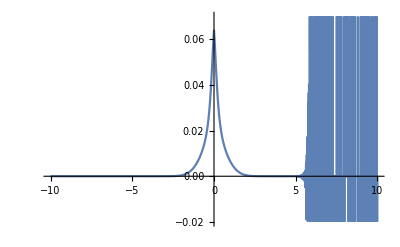

```mathematica
Plot[E1'[x]*E2[x]/50,{x,-10,10},PlotRange-> {{-10,10},{-0.02,0.07}}]
```

EIGENVALUES:

```mathematica
ϵ1[x_]:=If[x>0,ϵ1p[x],ϵ1m[x]];
ϵ2[x_]:=If[x>0,ϵ2p[x],ϵ2m[x]];
```

NONADIABATIC COUPLING

```mathematica
d12[x_]:=E1'[x]*E2[x];
```

```mathematica
d21[x_]:=-d12[x];
```

CURRENT POTENTIAL SURFACE “VC”

```mathematica
VC[x_]:=If[x≥ 0.3,ϵ2[x],ϵ1[x]];
```

```mathematica
curv=Plot[{ϵ1[x],ϵ2[x]},{x,-10,10},PlotRange-> Automatic];
```

```mathematica
ani = Animate[Show[curv,Graphics[{PointSize[Large],Red,Point[Dynamic[{t,VC[t]}]]}]],{t,-10,10,AppearanceElements->None}]
```

```mathematica
Export[NotebookDirectory[]<>"single.gif",ani]
```

/home/yyang173/Desktop/single.gif